Heat Equation Solution

```mathematica
heatEq = D[u[x, t], t] == D[u[x, t], {x, 2}];
```

Boundary conditions

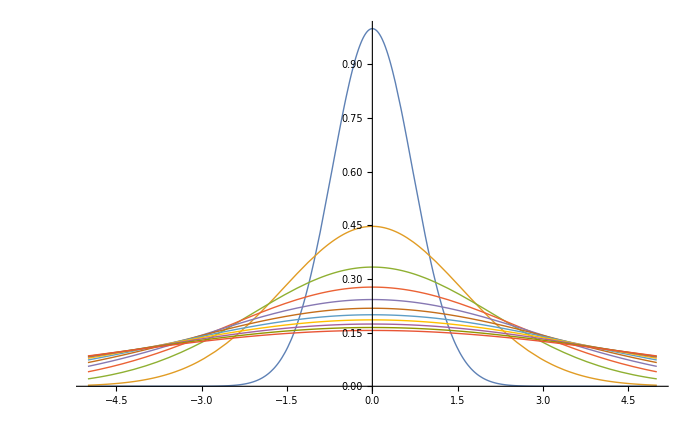

```mathematica
initCond = u[x, 0] == Exp[-x^2];
solution = DSolveValue[{heatEq, initCond}, u[x, t], {x, t}];
Plot[Evaluate[Table[solution, {t, 0,10}]],{x, -5, 5},
PlotRange-> All, PlotStyle->Thin
]
```

```mathematica
Plot3D[solution, {x, -10, 10}, {t, 0, 10}]
```

-Graphics3D-

```mathematica
(*initCond = u[x, 0] ==Exp[-x^4];
solution = DSolveValue[{heatEq, initCond}, u[x, t],{x,t}];
Plot[Evaluate[Table[solution, {t, 0,10, 1}]],{x, -10, 10},
PlotRange-> All, PlotStyle->Thin
]*)
```